03

哈密顿力学

拉格朗日力学相当成功，特别对于处理约束体系。那么，“既生瑜，何生亮？” ，为何还要学哈密顿力学？

哈密顿力学对后来的物理发展影响更大 —— 量子力学、固体物理均以哈密顿形式出现。

这是为什么鸭？—— 哈密顿形式具有对称性

（还是不懂啊？不要紧，这句话如同桃花岛黄老邪的“碧海潮生曲”，武功低的听了都被镇住了。）

对纠缠不清的，可以引用老杨说的，物理学几大方向：对称性、量子化、相位

本章拟在让你和哈密顿形式有个或许是第一次蜻蜓点水般的亲密接触。

## § 3.1 哈密顿力学

### § 3.1.1 相空间（phase space)

返回那张图：

牛顿力学在物理空间中讨论质点系的运动

拉格朗日力学在位形空间中讨论质点系的运动（为何要在位形空间？有何优点？）

哈密顿力学在相空间中讨论质点系的力学。      下面来体会体会什么是相空间、为什么要到相空间。

看拉格朗日方程（先看无约束体系）：

ⅆ/ⅆt(∂L(q,q̇,t))/(∂(q̇)_β)-(∂L(q,q̇,t))/(∂q_β)=Q_β^curl ,    β=1,2,…,D,     Q_β^curl  表示广义非保守力

这里以什么为自变量（独立变量）—— 广义坐标 q，广义速度 q̇，时间 t

思考：我们的解 q=q(t),  q̇=ⅆq/ⅆt 显示  q̇ 是 q 的对时间求导，如何理解 q̇ 和 q  是相互独立？

这似乎是拉格朗日力学相对于牛顿力学在理解上的一个坎。

在求解运动方程之前，我们并不知道  q̇ 和 q 有何关系，

物理告诉我们，在位置 q 处，  q̇  可以是任意的，反之亦然。（不同初始条件就可以做到这一点）

拉格朗日力学，就是先假设它们毫无关系（不存在函数关系，因为我们还没有利用任何定律、条件）

但它们总要满足“将它们视为独立变量的”拉格朗日方程

再由拉格朗日方程、初始条件，求出 q̇ 和 q 之间的关系。

先假定它们没关系，写出并求解方程，找出它们有关系。逻辑上矛盾？No！

正如无罪推断，先假设嫌疑人和罪无关，再找他与罪的关系。

千万别走火入魔，以至于连 ∂L(q,q̇,t)/∂t 也不理解，别被下面的胡搅蛮缠绕晕了。

数学上，这个偏导数的含义是：保持 q, q̇ 不变，时间微变，求变化率。

那么问题来了，我们的解是  q=q(t),  q̇=ⅆq/ⅆt=q̇(t)

时间微变了，怎么可能保持 q,  q̇ 不变？那又怎么求偏导？

哈密顿力学要以广义坐标 q，广义动量 p 为独立变量。

那又咋样？ q̇ 和 p 不就差个常数质量（非相对论力学中质量为常量）？   NO！

这里的 p_α=(∂L(q,q̇,t))/(∂(q̇)_α) （定义式） 是广义动量（在相空间中称为正则动量），不是简单的机械动量。

—— 记得只有直角坐标系（s-系）才有 P_α=M_α(q̇)_α

也记得即使在 s-系，电磁场中正则动量  p⃗=m OverDot[r⃗]+q^(e)A⃗ ≠ m OverDot[r⃗]

这一变有何好处：（目前所能想到的几点，还尚为粗浅，更本质的好处见后续讨论）

记得量纲一节： 广义动量与广义坐标之积的量纲与广义坐标系的选择无关！

这样，我们在称之为“一对共轭量”时心里就踏实些（对称性）

怎么理解量纲不变：虚功  ∑_β Q_β δq_β=∑_α F_α δs_α  ⟹     Q_β=∑_α F_α(∂s_α)/(∂q_β)

⟹   P_β=∑_α p_α(∂s_α)/(∂q_β)        ⟹   P_β δq_β 的量纲与坐标系无关，与坐标分量无关

广义速度（听起来像个矢量）在不同广义坐标系中的变换关系 与广义力的变换关系不同，

而广义动量的变换关系与广义力相同        ——  似乎又是与对称性有关

为下学期的统计力学夯实基础

因为在半经典统计力学中，微观态数正比于相空间体积，那么，这个

相空间体积在不同广义坐标系中应该有相同的量纲（否则比例系数量纲不确定）

最后发现，居然量子力学中的测不准关系也是针对坐标与动量

并非针对广义坐标与广义速度（当然，后两点都是事后诸葛）

最为重要的，在相空间讨论问题，提供了一种更为普适的变换可能性，以便通过变换求解问题。_

什么是相空间：由 D 个广义坐标 q 和 D 个广义动量 p 构成的 2D 维空间（D 是自由度)

相空间中确定了一点，就确定了每一个质点的位置与动量。

这样，因为每对共轭的广义坐标和广义动量的乘积量纲相同，

相空间的体积（  D 个广义坐标和 D 个广义动量的乘积），相空间体积的量纲就确定了。

不妨试试若用D 个广义坐标和 D 个广义速度构成相空间，相空间体积还会与广义坐标系无关吗？

至少这一点为统计力学的描述开方便之门（或者说，统计力学选择用相空间描述粒子状态）。

当然，这不是说拉氏力学就完全为哈氏力学所替代，在场论的许多场合，拉氏力学还有其便利之处。

正如牛顿力学某些情况下还是有便利之处。思考：请举例说明是什么情况

有阻尼力、摩擦力、复杂约束等情况，特别是体系中有些质点受到阻尼力，有些无阻尼。

在相空间中，q_α 称为第 α 个正则坐标，对应的 p_α 称为第 α 个正则动量，q_α, p_α 称为正则共轭，也称一对共轭变量

有时，也把 q, p 通称为相空间的正则坐标（因为它们都是相空间中的坐标）

哈密顿力学就是牛顿力学在相空间的描述形式。正如拉格朗日力学是位形空间中的描述形式。

既然以正则坐标 q, p 为独立变量，接着就应该把广义速度用正则动量（广义动量）替代。

p_α=(∂L(q,q̇,t))/(∂(q̇)_α)=p_α(q,q̇,t)       ⟹^(？？？)        (q̇)_α= (q̇)_α(q,p,t) ， α=1,2,…,D

左边定义了正则动量，能否反过来唯一确定广义速度？

若能建立起它们之间的一一对应，一旦求解了正则坐标和正则动量，广义速度也就得解了。

那么上式从 p_α(q,q̇,t)  到 (q̇)_α(q,p,t) 的变换是否存在？（能否求得反函数，是否可逆？）

变换存在的充要条件是以下雅克比行列式不为 0

|(∂p)/(∂q̇)|≠0,    (其中矩阵元   [(∂p)/(∂q̇)])_αβ≡(∂p_α(q,q̇,t))/(∂(q̇)_β)=(∂^2 L(q,q̇,t))/(∂(q̇)_β∂(q̇)_α)

那么，这个雅克比是否为 0？

##### 关于雅克比行列式与变换关系的一一对应

这里的雅克比行列式 J 只涉及一阶偏导数，又是个线性代数中的行列式，似乎仅适合于线性问题，其实是这样的：

对某一组特定的广义速度 (q̇)^(0) ，若 J((q̇)^(0))≠0，则存在一组 p^(0) 与 (q̇)^(0)一一对应

对另一组特定的广义速度 (q̇)^(1)，则要求 J((q̇)^(1))≠0，才能保证存在一组 p^(1) 与 (q̇)^(1)一一对应

若对 q̇ 的某个区域 A_(q̇) ，都有 J(q̇)≠0， q̇∈A_(q̇)，就存在某个区域 A_p 的 p， 与区域 A_(q̇)中 的 q̇ 一一对应

点点对应 到 区域区域对应，与变换是否线性无关。

如果你一直放不下线性的概念，那么，可以理解为：在任意一点的邻域，总是可以看成线性的。

雅克比行列式不为 0，是在某大区域中的每一个点都成立的，也就是每个点，都建立了一一对应。

简而言之，雅克比行列式研究某点邻域的性质，在那一点是否能建立一一对应关系，由其邻域性质决定。

从 p_α=p_α(q,q̇,t)  到   (q̇)_α= (q̇)_α(q,p,t) 的可逆性由以下数学定理保证。

动量可逆性定理：

矩阵 (∂^2 L(q,q̇,t))/(∂(q̇)_β∂(q̇)_α)是非奇异的，因此 p_α=p_α(q,q̇,t)  到   (q̇)_α= (q̇)_α(q,p,t)是可变换的

证明：

在一般广义坐标系中，拉格朗日量为（见 § 2.1.3）

L(q,q̇,t)=T_2(q,q̇,t)+T_1(q,q̇,t)+T_0(q,t)-U(q,t)

记得此式是从 s-系到 q-系导出来的，

其中 T_2,T_1, T_0 为 q̇ 的齐二次，齐一次和齐零次项表达式

因此，(∂p_α(q,q̇,t))/(∂(q̇)_β)=(∂^2 L(q,q̇,t))/(∂(q̇)_β∂(q̇)_α)= m_αβ(q,t)=(∑_(γ=1))^d M_γ(∂s_γ(q,t))/(∂q_α)(∂s_γ(q,t))/(∂q_β)

注意 s 系是直角坐标系

上方程可改写为矩阵的乘积形式

m_αβ(q,t)=(∑_(γ=1))^d M_γ(∂s_γ(q,t))/(∂q_α)(∂s_γ(q,t))/(∂q_β)=(∑_(γ=1))^d(∂s_γ(q,t))/(∂q_α)(∑_(θ=1))^d M_γ δ_(γ θ)(∂s_θ(q,t))/(∂q_β)=(∑_(γ=1))^d(∑_(θ=1))^d X_(α γ)Y_(γ θ)Z_(θ β)=X Y Z

X_(α γ)=(∂s_γ(q,t))/(∂q_α)=( [(∂s)/(∂q)]^T )_(α γ)     ⟹    X= [(∂s)/(∂q)]^T

Y_γ_θ=M_γ δ_(γ θ)  （对角矩阵）      ⟹      Y=M̃                   由质量 M_α 构成的对角矩阵

Z_(θ β)=(∂s_θ(q,t))/(∂q_β)=[(∂s)/(∂q)]_(θ β)              ⟹      Z= [(∂s)/(∂q)]

⟹       [(∂p)/(∂q)]=[(∂s)/(∂q)]^T M̃ [(∂s)/(∂q)] ,      (其中对角阵   [M̃])_αβ=M_α δ_αβ

两边同取行列式，并利用矩阵转置不改变行列式的值及方矩阵积的行列式等于各自行列式的积，即得

|(∂p)/(∂q)|=(|(∂s)/(∂q)|)^2(M_1 M_2(…M)_D)^对角阵的行列式>0           ——  雅克比不为 0

这里默认 q 是好坐标，|(∂s)/(∂q)|≠0

还可以证明，矩阵(∂p)/(∂q) 是正定的，即：

对任意非 0 矢量 x, 有：[x]^T[(∂p)/(∂q)][x]>0

注意行列式大于 0 并不意味着矩阵是正定的。（(存在非 0 本征值)_(⏟_非幂零矩阵)且所有的本征值都不小于 0  ）

动量可逆性定理表明，拉格朗日量总可以写成：L(q,q̇,t)=L̃(q,p,t) 形式

更一般的，任何广义坐标和广义速度的函数：f(q,q̇,t) 总可以写成

f(q,q̇,t)=f[q,q̇(q,p,t)t]

所以，物理（力学）量总可以写成相空间正则坐标、正则动量的函数。

那么，如何从 p_α=p_α(q,q̇,t)  反求 (q̇)_α= (q̇)_α(q,p,t)？

对质点系 —— 求解线性方程组

在一般广义坐标系中，拉格朗日量为

L(q,q̇,t)=T_2(q,q̇,t)+T_1(q,q̇,t)+T_0(q,t)-U(q,t)

T_2(q,q̇,t)=1/2(∑_(γ=1))^d(∑ _(ζ=1))^d m_(γ ζ)(q,t)(q̇)_γ(q̇)_ζ
                 m_(γ ζ)(q,t)=(∑_(β=1))^d M_β(∂s_β(q,t))/(∂q_γ)(∂s_β(q,t))/(∂q_ζ)
T_1(q,q̇,t)=(∑_(γ=1))^d n_γ(q,t)(q̇)_γ
                  n_γ(q,t)=(∑_(β=1))^d M_β(∂s_β(q,t))/(∂q_γ)(∂s_β(q,t))/(∂t)
T_0(q,t)，U(q,t) 与 q̇ 无关

从而：p_α=(∂L(q,q̇,t))/(∂(q̇)_α)=(∑_(β=1))^D m_(α β)(q,t)(q̇)_β+n_α(q,t)

是一个线性方程组：(∑_(β=1))^D m_(α β)(q,t)(q̇)_β=p_α-n_α(q,t)

动量可逆性定理表明系数矩阵  m_(α β)(q,t)=(∂p_α(q,q̇,t))/(∂q_β) 是非奇异的，故有唯一解。

这是一个一般性证明，对具体问题，只需把每一个正则动量根据定义求出来，反过来求广义速度。

对非质点系 （场）——  需要是 well-defined 拉格朗日体系

广义动量依然是：p_α=(∂L(q,q̇,t))/(∂(q̇)_α)=p(q,q̇,t)

若它可反解求出： (q̇)_α= (q̇)_α(q,p,t)

则称为定义明确 (well-defined) 的拉格朗日体系

### § 3.1.2 哈密顿方程

接着，我们来推导在相空间中运动方程的形式，出发点当然是位形空间的拉格朗日形式。

来看广义能量函数（记得“吹皱一池春水，干卿何事”），它定义为

H(q,q̇,t)=(∑_(β=1))^D(∂L(q,q̇,t))/(∂(q̇)_β)(q̇)_β-L(q,q̇,t)         这是定义，广义能量函数是 q, q̇,t 的函数

提起广义能量函数（"吹皱一池春水，干卿何事"），除了定义式，应该还能想起三点

i)      在 s-系，它是机械能，在一般的 q-系，未必是机械能；

ii)    不同广义坐标系中   H_q(q,q̇,t) ≠ H_s[s(q,t),ṡ(q,q̇,t), t] ，这点与拉格朗日量不同；

iii)   什么条件下才有      H_q(q,q̇,t) = H_s[s(q,t),ṡ(q,q̇,t), t]  ?          变换不显含时间 s_α=s_α(q)

接着，做 (q̇)_α= (q̇)_α(q,p,t) 的替代（这是上一小节的铺垫：动量可逆性定理），得：

H(q,q̇,t)=H[q,(q̇)_α(q,p,t),t]=H̃(q,p,t)

这里的顶标“~”仅是为了强调函数关系的不同，我们以后就略去这个顶标

这样我们就把广义能量函数写成相空间变量（正则坐标和正则动量）的函数。

当我们将它写成相空间正则坐标的函数时，我们称之为哈密顿量（陈近南出场了）。

所以，广义能量函数与哈密顿量是一个物理量，只不过其自变量不同（函数关系自然也不同）。

现在来看广义能量函数的全微分（注意它以 q, q̇,t 为自变量）

ⅆH=ⅆ[(∑_(β=1))^D(∂L(q,q̇,t))/(∂(q̇)_β)(q̇)_β-L(q,q̇,t)]_(这是广义能量函数 的定义)          记得 (∂L(q,q̇,t))/(∂(q̇)_β)=p_β （这也是定义）
=[(∑_(β=1))^D ⅆ(p_β(q̇)_β)]-ⅆL(q,q̇,t)
=(∑_(β=1))^D[p_β ⅆ(q̇)_β+(q̇)_β ⅆ p_β-(∂L(q,q̇,t))/(∂q_β)ⅆ q_β-((∂L(q,q̇,t))/(∂(q̇)_β))^(⏞^p_β)ⅆ(q̇)_β]-(∂L(q,q̇,t))/(∂t)ⅆt          下划线的两项相消
接着利用{拉格朗日方程：ⅆ/ⅆt[(∂L(q,q̇,t))/(∂(q̇)_β)]^p_β-(∂L(q,q̇,t))/(∂q_β)=0 
广义功能定理：Ḣ=-(∂L(q,q̇,t))/(∂t)     }  外力为保守力的情况
ⅆH=(∑_(β=1))^D((q̇)_β ⅆ p_β-(ṗ)_β ⅆ q_β)+Ḣ ⅆt

如果直接将 H 写成 q,p,t 的函数（即，从哈密顿量出发），则

ⅆH(q,p,t )=(∑_(β=1))^D[(∂H(q,p,t))/(∂q_β)ⅆ q_β+(∂H(q,p,t))/(∂p_β)ⅆ p_β]+(∂H(q,p,t))/(∂t)ⅆt

比较蓝色、紫色两式，并注意到偏导数时将 q,p,t 三者视为独立变量，即可得哈密顿方程

(q̇)_β=(∂H(q,p,t))/(∂p_β)，  (ṗ)_β=-(∂H(q,p,t))/(∂q_β)，  Ḣ=(∂H(q,p,t))/(∂t)， β=1,2,…,D

运动方程退化为两组关于相空间变量（正则坐标）q_k, p_k的一阶微分方程。

前两个等式显示了某种对称性，除了有个正负号的区别。

这里我们从拉格朗日方程“导出”哈密顿方程，注意到推导是可逆的，故有

牛顿方程   ⟺    拉格朗日方程   ⟺^  哈密顿方程    （参见本章最后的例题 3.3.02）

即，三者等价。但是记住狄拉克说过：

It is not always so that theories which are equivalent are equally good.

其实，“三个”哈密顿方程式中只需前“两个”即可求解

但最后一个方程：ⅆH/ⅆt=(∂H(q,p,t))/(∂t) 与拉氏力学中的广义功能定理：ⅆH/ⅆt=-(∂L(q,q̇,t))/(∂t)类似

通常用于得到运动积分（守恒量），简化求解过程。

实际上，第三个方程可以从前两组方程导出（不独立）

Ḣ=(ⅆH(q,p,t))/ⅆt=(∑_(β=1))^D[(∂H(q,p,t))/(∂q_β)(q̇)_β+(∂H(q,p,t))/(∂p_β)(ṗ)_β]+(∂H(q,p,t))/(∂t)
=(∑_(β=1))^D[-(ṗ)_β(q̇)_β+(q̇)_β(ṗ)_β]+(∂H(q,p,t))/(∂t)=(∂H(q,p,t))/(∂t)

关于 Ḣ  的几个方程

ⅆH/ⅆt=(∂H(q,p,t))/(∂t)   和     ⅆH/ⅆt=-(∂L(q,q̇,t))/(∂t)      （哈密顿方程和广义功能定理）

尽管左边相同，都为哈密顿的时间变化率，但右边的函数、自变量、正负号都不同。

计算右边时需特别注意  (∂H(q,p,t))/(∂t)=^(？？)(∂H(q,q̇,t))/(∂t)  两边一般未必相等，因为

Ḣ=(∂H(q,p,t))/(∂t) =-(∂L(q,q̇,t))/(∂t)   但通常：Ḣ≠(∂H(q,q̇,t))/(∂t)

还有：((ṗ)_β=-(∂H(q,p,t))/(∂q_β))_哈密顿方程=((ṗ)_β=(∂L(q,q̇,t))/(∂q_β))_拉格朗日方程

⟹       (∂H(q,p,t))/(∂q_β) =-(∂L(q,q̇,t))/(∂q_β)≠ (∂H(q,q̇,t))/(∂q_β)                最右边的 H 写成广义坐标及广义速度的函数

另外，还需注意以上等式成立的条件

对称性？

哈密顿方程：(q̇)_β=(∂H(q,p,t))/(∂p_β)，  (ṗ)_β=-(∂H(q,p,t))/(∂q_β)    一正一负，也叫对称？

真空中的Maxwell方程：∇×B⃗=(∂E⃗)/(∂t)，∇×E⃗=-(∂B⃗)/(∂t)     也称电磁对称啊

M.V.Berry 称之为“电磁民主” ( electric-magnetic democracy )

负号在哪里？

哈密顿方程：(q̇)_β=(∂H(q,p,t))/(∂p_β)，  (ṗ)_β=-(∂H(q,p,t))/(∂q_β)，一正一负，哪一个含负号

理解：在 s-系，H=T+U,   (∂T)/(∂s_β)=0     ⟹      (∂H)/(∂s_β)=(∂U)/(∂s_β)=-F_β=-(ṗ)_β

注：某种意义上，拉格朗日量 L=T-U 中的负号可以理解为来自保守力的定义 -∇U

如保守力定义为 ∇Φ，则 L=T+Φ,    H=T-Φ,  但还是有   (ṗ)_β=-(∂H(q,p,t))/(∂q_β)

所以这个负号应该反映某个物理本质，不仅仅是人们的约定。

正如，真空中的Maxwell方程：∇×B⃗=(∂E⃗)/(∂t)，∇×E⃗=-(∂B⃗)/(∂t)，若负号消失，就不再存在电磁波。

思考：若 (ṗ)_β=-(∂H(q,p,t))/(∂q_β)中的负号消失，会有什么物理后果？

例 3.1.01

球对称简谐势场中的质点，在球坐标系中求哈密顿及运动方程

解：

球坐标系： {q_1=r
q_2=θ
q_3=ϕ     中的拉格朗日

L(q,q̇,t)=1/2 m( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)-1/2 k r^2

化成相空间正则坐标的函数，需利用广义动量的定义

{p_1=(∂L(q,q̇,t))/(∂ṙ)=m ṙ
p_2=(∂L(q,q̇,t))/(∂θ̇)=m r^2 θ̇
 p_3=(∂L(q,q̇,t))/(∂ϕ̇)=m r^2 sin^2 θ ϕ̇     从p_α_=p_α(q,q̇,t)  求 (q̇)_α= (q̇)_α(q,p,t)
                          的确是求解线性方程组

求得：     ṙ=p_1/m,   θ̇=p_2/(m r^2),   ϕ̇=p_3/(m r^2 sin^2 θ)                                              (#)

广义能量函数：

H(q,q̇,t)=(∑_(β=1))^3 p_β(q̇)_β-L(q,q̇,t)=1/2 m( (ṙ)^2+r^2 (θ̇)^2+r^2 sin^2 θ (ϕ̇)^2)+1/2 k r^2

哈密顿量（广义速度 ⟶ 关于动量）

H(q,p,t)=p_1^2/(2m)+p_2^2/(2m r^2)+p_3^2/(2m r^2 sin^2 θ)+1/2 k r^2

哈密顿方程：(q̇)_β=(∂H(q,p,t))/(∂p_β)

ṙ=p_1/m,     θ̇=p_2/(m r^2),      ϕ̇=p_3/(m r^2 sin^2 θ)  与上面绿色方程 (#) 相同

原来第一组哈密顿方程对应于广义动量的定义式！（ 回顾动量可逆性定理）

另一组哈密顿方程：(ṗ)_β=-(∂H(q,p,t))/(∂q_β)

(ṗ)_1=-(∂H)/(∂r)=p_2^2/(m r^3)+p_3^2/(m r^3 sin^2 θ)-k r,    (ṗ)_2=-(∂H)/(∂θ)=(p_3^2 cos θ)/(m r^2 sin^3 θ),       (ṗ)_3=-(∂H)/(∂ϕ)=0                (†)

记得还有一个：Ḣ=(∂H(q,p,t))/(∂t)=0 , 因为  H(q,p,t)不显含时间 t

p_1^2/(2m)+p_2^2/(2m r^2)+p_3^2/(2m r^2 sin^2 θ)+1/2 k r^2=H_0   能量是运动常数（运动积分）

H_0 初始时刻的哈密顿量，以初始时的正则坐标代入即可。

此外注意 p_3=p_ϕ =m r^2 sin^2 θ ϕ̇   也是运动常数（见方程 (†)），因为

从拉格朗日力学来看 ϕ 是可遗坐标 。从哈密顿力学来看   (ṗ)_3=-(∂H(q,p,t))/(∂q_3)=0

注：若取 s-系，有几个守恒量？仅 H 一个，故守恒量个数与坐标系（相空间）的选择有关

为何守恒量也称运动积分？为什么运动积分很重要？

X 守恒  ⟹  ⅆX/ⅆt=0   (⟹^全微分形式)_可直接积分   X=C，     C 由初始条件确定

一个质点系有 D 个自由度，若有 C 个几何约束（完整约束），其自由度 f=D-C

若能得到 f 个运动积分，则体系在以下意义上是容易求解的。

求解代数方程，将体系所有的待解物理量都表示为某一个广义坐标的函数，

从而对应于此广义坐标的广义速度也可表为该广义坐标的函数：q̇=f(q)，

因此可以积分求解出 q(t) （尽管解未必能表示为初等函数）。

这是朴素的理解。后续还会有新形式的理解。

### § 3.1.3 约束条件下的约化哈密顿量

上一小节为方便理解，假设了只存在保守力。

当存在非保守力时，拉格朗日方程和广义功能定理分别为

(ṗ)_β= (∂L(q,q̇,t))/(∂q_β)+Q_β^(curl),    Ḣ=- (∂L(q,q̇,t))/(∂t)+(∑_(β=1))^D Q_β^(curl)(q̇)_β

和上一小节的区别在于，现在存在非保守力，这时应利用

拉格朗日方程：ⅆ/ⅆt[(∂L(q,q̇,t))/(∂(q̇)_β)]-(∂L(q,q̇,t))/(∂q_β)=Q_β^(curl)       非保守广义力

广义功能定理：Ḣ=(∑_(β=1))^D Q_β^(curl)(q̇)_β-(∂L(q,q̇,t))/(∂t)

差别仅在于多了非保守力项 Q_β^(curl)，类似可以导得“三个”哈密顿方程式为：

(q̇)_β= (∂H(q,p,t))/(∂p_β),      (ṗ)_β=-(∂H(q,p,t))/(∂q_β)+Q_β^(curl)

Ḣ= (∂H(q,p,t))/(∂t)+(∑_(β=1))^D Q_β^(curl)(q̇)_β(q,p,t)                    （想不想不再看公式，试一试自己推导）

当所有非保守力均来自约束力且约束力对虚位移不做虚功（全保守零虚功）时，则有：_

(q̇)_β= (∂H(q,p,t))/(∂p_β),   (ṗ)_β=(-(∂H(q,p,t))/(∂q_β))_保守力+((∑_(a=1))^C λ_a(∂G_a(q,t))/(∂q_β))_约束力

注：(ṗ)_β 方程右边分为保守力项与约束力项，更多地是在于帮助理解。

记得：(ṗ)_β=-(∂H(q,p,t))/(∂q_β)=(∂L(q,q̇,t))/(∂q_β)=-(∂U)/(∂q_β) ≠ (∂H(q,q̇,t))/(∂q_β)

Ḣ=(∂H(q,p,t))/(∂t)=-(∂L(q,q̇,t))/(∂t)≠(∂H(q,q̇,t))/(∂t)     注意等式成立的条件

Ḣ= (∂H(q,p,t))/(∂t)-(∑_(a=1))^C λ_a(∂G_a(q,t))/(∂t)       其中G_a(q,t)=0, a=1,2,…, C为 C 个独立的约束方程。

（想不想自己推导一下？）(ṗ)_β 方程右边绿色项即 Q_β^(curl)，再补∂G_a(q,t)/∂t，凑 ⅆG_a(q,t)/ⅆt=0

当存在约束时，如果是完整约束，人们可以通过约束方程消去受限坐标，只留下自由坐标。

这时，哈密顿方程是否形式上还是相同的呢？

记得   消去受限坐标后，拉格朗日量变成约化的 (reduced) 拉格朗日量，拉格朗日方程形式不变

对几何约束，广义能量函数可以由约化的拉格朗日定义，因此（这里以顶标 ~ 表示约化量）

H̃=H̃(q^(f),(q̇)^(f),t)=(∑_(β=1))^(D-C)(∂L̃(q^(f),(q̇)^(f),t))/(∂(q̇)_β^(f))(q̇)_β^(f)-L̃(q^(f),(q̇)^(f),t)

H̃=(∑_(β=1))^(D-C)(p̃)_β^(f)(q^(f),(q̇)^(f),t)(q̇)_β^(f)-L̃(q^(f),(q̇)^(f),t)

其中   (p̃)_β^(f)=(p̃)_β^(f)(q^(f),(q̇)^(f),t)=(∂L̃(q^(f),(q̇)^(f),t))/(∂(q̇)_β^(f))

这时仍可用正则动量消去广义能量函数中的广义速度得到约化的哈密顿

而哈密顿方程仍有相同的形式

(q̇)_β^(f)=(∂H̃(q^(f),(p̃)^(f),t))/(∂(p̃)_β^(f)),     OverDot[p̃]_β^(f)=-(∂H̃(q^(f),(p̃)^(f),t))/(∂q_β^(f)), β=1,2,…,D-C

OverDot[H̃]=(ⅆ H̃)/ⅆt=(∂H̃(q^(f),(p̃)^(f),t))/(∂t)

其实这个性质是拉格朗日形式和哈密顿形式的优越性所在。

哈密顿形式继承了拉格朗日形式的有点。还要发扬光大。继承发扬

当然，这里还是涉及能否从正则动量

(p̃)_β^(f)=(p̃)_β^(f)(q^(f),(q̇)^(f),t)=(∂L̃(q^(f),(q̇)^(f),t))/(∂(q̇)_β^(f))

出发，反求出广义速度  (q̇)_β^(f)=(q̇)_β^(f)(q^(f),(p̃)^(f),t) 的问题。

如果反函数存在，则可将约化广义能量函数写成约化哈密顿量

H̃(q^(f),(q̇)^(f),t)=H̃(q^(f),(q̇)^(f)(q^(f),(p̃)^(f),t),t)

记住：左边称为约化的广义能量函数

右边称为约化的哈密顿量      —— 其实就自变量改变而已

这个反函数的存在性还是依赖于雅克比。

|(∂(p̃)^(f))/(∂(q̇)^(f))|≠0,     其中： [(∂(p̃)^(f))/(∂(q̇)^(f))]_(α β)≡ (∂(p̃)_α^(f))/(∂(q̇)_β^(f))=(∂^2 L̃(q^(f),(q̇)^(f),t))/(∂(q̇)_β^(f)∂(q̇)_α^(f))

在机器学习中，绿色项称为 黑塞矩阵 Hessian matrix

这个雅克比行列式不为 0 的证明，就是约化动量可逆性定理。

该定理还证明了矩阵  [(∂(p̃)^(f))/(∂(q̇)^(f))]_(α β)  是正定矩阵，因而是非奇异矩阵，

从而保证了可以利用广义动量表达式将广义速度表为正则动量的函数。_最后

试比较：正则坐标 vs 广义坐标，正则动量 vs 广义动量，_广义能量函数 vs 哈密顿量

如果你在当时，能否想到再进一步，用广义动量替代广义速度作为独立变量？_

当然，至此的哈氏力学尚只是“继承”，还未“发扬”，接着的几节将会“发扬”。

本节小结：

哈密顿量就是以正则坐标、正则动量为自变量的广义能量函数；（这里涉及能否这么做、怎么做）

不同广义坐标系可构成不同的相空间（ 2D 维），拉格朗日力学中称为不同的位形空间（ D 维），

运动方程为哈密顿方程：(q̇)_β= (∂H(q,p,t))/(∂p_β),   (ṗ)_β=-(∂H(q,p,t))/(∂q_β)， Ḣ= (∂H(q,p,t))/(∂t)  （对保守力体系，包括约化量）

第一组方程通常与广义动量的定义一致（其实就是广义动量表示为广义坐标、广义速度的函数的反函数）

哈密顿方程与拉格朗日方程在描述质点动力学上等价，都等价于牛顿方程；

哈密顿方程在不同相空间中也具有协变性，对几何约束消去受限坐标后，约化哈密顿量对应的方程也具有协变性

至此，哈密顿力学只是继承了拉格朗日力学（另一种力学新形式），尚未发扬光大。

但至此我们看到，哈密顿方程的形式让“可遗坐标”与“运动常数”的关系暴露无遗。例如：(ṗ)_β=-(∂H(q,p,t))/(∂q_β)

接着探索哈密顿力学优势所在。

## § 3.2 泊松括号 正则变换 生成函数

为讨论哈密顿力学相对于拉格朗日力学的优势所在，需要一点数学。

### § 3.2.1 泊松括号

在哈密顿力学中，所有的物理力学量都表示成相空间变量（正则坐标、正则动量）的函数

f(q,p,t)=f(q,q̇(q,p,t),t)     右边表示广义速度 q̇ 表示为正则动量 p 的函数，消去 q̇

这一点有动量可逆性定理保驾护航。

假设体系不存在约束，那么正则坐标和正则动量由哈密顿方程式联系起来

(q̇)_β= (∂H(q,p,t))/(∂p_β),   (ṗ)_β=-(∂H(q,p,t))/(∂q_β),      Ḣ= (∂H(q,p,t))/(∂t)  =-(∂L(q, q̇,t))/(∂t)=Ḣ

（第三式分别为哈密顿方程和广义功能定理，左右两端的 H 各以什么为自变量，两端相等吗？）

注意这组方程成立的条件（没有非保守力）

当然也要了解：存在非保守力如何、存在约束时方程会多出哪一些项

（其实存在约束时，哈密顿力学未必有拉格朗日力学好用，正如存在阻尼时后者没有牛顿好用）

以上方程实际上都涉及时间变化率。

那么，人们会想，一般物理量 f(q,p,t) 的时间变化率咋求？

ḟ(q,p,t) ≡(ⅆf(q,p,t))/ⅆt       利用多元函数的求导法则
=(∑_(α=1))^D[(∂f(q,p,t))/(∂q_α)(q̇)_α+(∂f(q,p,t))/(∂p_α)(ṗ)_α]+(∂f(q,p,t))/(∂t)
=((∑_(α=1))^D[(∂f(q,p,t))/(∂q_α) (∂H(q,p,t))/(∂p_α)-(∂f(q,p,t))/(∂p_α)(∂H(q,p,t))/(∂q_α)])_(⏝^)+(∂f(q,p,t))/(∂t)

无论什么物理（力学）量，表示为相空间变量 p, q 的函数之后，都通过这个方程形式求时间变化率。

为此引入约定符号 [f,g]，定义为

[f,g]≡(∑_(α=1))^D[(∂f(q,p,t))/(∂q_α) (∂g(q,p,t))/(∂p_α)-(∂f(q,p,t))/(∂p_α)(∂g(q,p,t))/(∂q_α)]

[f,g]  称为 泊松括号，对两个相空间坐标函数求泊松括号，结果当然还是相空间坐标的函数

利用泊松括号，则任意物理量的时间变化率可写成

ḟ(q,p,t)≡(ⅆf(q,p,t))/ⅆt=[f,H]+(∂f(q,p,t))/(∂t)

是不是很量子力学？——  神似！

其实从经典力学到量子力学的一个过渡，可以视为将泊松括号中的物理量函数换成算符，这是后话。

并不是在量子力学出现之后，人们将经典力学的形式往量子力学形式趋同，

经典力学在量子力学出现之前，就被数学家写成这个形式。

当然，这里也不能说量子力学是这些伟大的数学家“玩”出来的。

——  毕竟，量子力学还是物理学家们玩出来的。

这有点类似于江湖上的世纪悬案：狭义相对论是爱因斯坦还是庞加莱 Poincaré 建立的？

即使是如今狭义相对论的数学形式，也是 庞加莱 早于爱因斯坦和闵可夫斯基建立。

上式表明，如果一个物理量不显含时间（比如动能、势能都可能不显含时间）那么

它是运动常数的充要条件是它与哈密顿量构成的泊松括号为 0。

量子力学中，物理量用算符表示，如果表示物理量的算符不显含时间

并且它与哈密顿算符对易，则该物理量是运动常数。_——  “ 似不似神似？”

泊松括号的性质：

泊松括号的定义：     [f,g]≡(∑_(α=1))^D[(∂f(q,p,t))/(∂q_α) (∂g(q,p,t))/(∂p_α)-(∂f(q,p,t))/(∂p_α)(∂g(q,p,t))/(∂q_α)]                 (1.1)

利用定义式 (1.EquationNumbered)易证以下性质（最后一个会繁琐一点）

[f,g]=-[g,f]        反对称，不满足交换律

[f,f]=0

[f,α g + β h]=α_[f,g]+β[f,h]
[f,g h]=[f,g] h_ + [f,h]g
[f,[g,h]]+[g,[h,f]]+[h,[f,g]]=0  }   雅克比恒等式，α, β 为常数
      （有的书雅克比恒等式是指最后一个）

最后一个可与矢量公式：a⃗×(b⃗×c⃗)+b⃗×(c⃗×a⃗)+c⃗×(a⃗×b⃗)=0     比较记忆

```mathematica
av={ax,ay,az};  bv={bx,by,bz};  cv={cx,cy,cz};  
tst=av×(bv×cv)+bv×(cv×av)+cv×(av×bv)//Simplify
```

{0,0,0}

哈密顿方程式也可以写成泊松括号形式（注意 q, p 是独立变量）

(q̇)_β= (∂H(q,p,t))/(∂p_β)        ⟺   (q̇)_β=[q,H]

(ṗ)_β=- (∂H(q,p,t))/(∂q_β)   ⟺   (ṗ)_β=[p,H]           终于把那个负号给隐起来了，看起来更对称了

Ḣ= (∂H(q,p,t))/(∂t)       ⟺    Ḣ= [H,H]+(∂H(q,p,t))/(∂t)   利用了 (1.EquationNumbered) 式

还有，更“量子力学”的雏形，对正则坐标 q_α和正则动量 p_β，有

[q_α,q_β]=0,         [q_α,p_β]=δ_(α β),        [p_α,p_β]=0

其中 δ_(α β) 是 Kroenecker delta 符号，满足 α=β 时 δ_(α β) =1， α≠β 时 δ_(α β) =0。

这三个式子以后也称为判断一个变换是否为正则变换的判据。

### § 3.2.2 正则变换

哈密顿力学有个重要特性：若不同广义坐标系的变换满足雅克比不为 0，则

不同广义坐标系中，哈密顿方程的形式不变。

但这个特性，拉格朗日力学也有：若不同广义坐标系的变换满足雅克比不为 0，则

不同广义坐标系中，拉格朗日方程的形式不变。

当然，还有第二种协变性：

就是对约束情况，约化的拉格朗日量或哈密顿量满足相同形式的方程。

到目前为止，以广义动量替代广义速度，从拉氏力学到哈氏力学，只看到“继承”，尚未见“发扬”。

貌似只给人们形式和心理上的满足：看上去很美，很对称，或称之“坐标-动量民主” (q-p democracy)。

哈密顿力学还有什么优点呢？

或者，为什么要从 D 维位形空间(configuration space)拓展到 2 D 维相空间(phase space)？

回想不同位形空间的变换是怎么变的：

在位形空间，总是先对广义坐标做变换：s_α=s_α(q,t)，

广义坐标的变换决定了广义动量的变换

p_α(q,q̇,t)=(∑_(β=1))^d P_β(∂s_β(q,t))/(∂q_α)     （P_α 和 p_β 分别为 s 系和 q 系的广义动量）

在这样的变换下，拉氏方程和哈氏方程形式都不改变。

而在相空间，广义坐标和广义动量地位是平等的（“坐标-动量民主”，这是其实引进相空间的目的与意义所在），

广义坐标和广义动量都被视为独立变量，共同描述粒子的运动状态。

思考：一个力学体系，总能求得 q(t) 进而 q̇(t) 再由动量可逆性定理 p(t)=f(q,q̇,t)，即，

p(t)总可以归结为 q 的函数，物体运动状态为何需要 广义坐标和广义动量共同描述？

因为初始条件不同，运动方程需要两初始条件才能确定解，所以需要广义坐标和广义动量。

那么，广义坐标和广义动量都被视为独立变量，从一个相空间到另一个相空间的变换，

未必要先变换广义坐标，再由广义坐标的变换关系决定广义动量的变换关系：p_α(q,q̇,t)=(∑_(β=1))^d P_β(∂s_β(q,t))/(∂q_α)

——  那就不“民主”、不“平等”、不“自由”了，体现不了社会主义核心价值观

就是说，既然哈密顿力学中将广义动量视为与广义坐标地位相同的独立自变量，_

广义坐标 q 和广义动量 p 似应“联立变换”：{q_α=_ q_α(P,Q)
p_α=_ p_α(P,Q) ，这也是形式上所期望的。_

原来，从 D 维 位形空间到 2D 维 相空间的一个好处是：不同相空间变换的花样多多了！

那么需要这么多令人眼花缭乱的变换？        ——   “乱花渐欲迷人眼”

这种“联立变换”的变换自由度当然比位形空间的坐标变换自由度大，因为

位形空间的变换是先对广义坐标作变换，q_α=q_α(r,t) ,

而广义坐标的变换决定了广义动量的变换

p_α^(q)(q,q̇,t)=(∑_(β=1))^d p_β^(r)(r,ṙ,t)(∂r_β(q,t))/(∂q_α)

而两者“联立变换”的意思是：{q_α=q_α(Q,P,t)
p_α=p_α(Q, P,t)           比较   {q_α=q_α(Q,t)    ⟹    Q_β=Q_β(q,t)
p_α=(∑_(β=1))^d P_β(∂Q_β)/(∂q_α)

广义动量的变换不再受制于广义坐标的变换，并且广义坐标的变换涉及广义动量 P。_

“联立变换”还有个优点：变换后的新正则坐标不再是物理空间的坐标、动量量纲（但应保持乘积的量纲不变）

或者说，将新的哈密顿量变得以尽可能少的正则坐标变量作为自变量的函数以便得到尽可能多的运动常数。

一个大胆的想法就是，把正则坐标直接变换成  “运动常数”，以运动常数作为新的相空间的正则坐标。

例如，在位形空间的变换中（称为点变换），广义坐标总是和质点位置相关，无论变换到什么广义坐标系。

而在像空间变换中，{q_α=q_α(Q,P,t)
p_α=p_α(Q, P,t)  ⟹    {Q_α=Q_α(q,p,t)
P_α=P_α(q, p,t)，

回顾任意力学量 f 都可表示成 q, p 的函数 f(q,p,t)，那么新的相空间的正则坐标 Q(q,p,t), P(q,p,t)，

就可以是任意的力学量。那么，

有没有这样一种可能，经过某种相空间变换，在新相空间中，所有正则坐标就是运动常数！

这么一来，不就实现了“中国梦”：  经过变换，每个正则坐标都是守恒量，

都可以由初始值确定，在经过反变换变回原来的坐标，原坐标岂不就得到解了。

要实现这个“中国梦”，需回答几个问题。

1.  变到新相空间时，怎么判断每一个坐标都是守恒量？_

回顾 § 3.1节最后“本节小节”中的一句话：

哈密顿方程的形式让“可遗坐标”与“运动常数”的关系暴露无遗。

(q̇)_β=(∂H(q,p,t))/(∂p_β)，      (ṗ)_β=-(∂H(q,p,t))/(∂q_β)

所以，为了使这些运动常数哈梅内伊未着寸缕地呈现，我们希望变换前后哈密顿方程形式不变

为何选择哈密顿（难道哈密顿和哈梅内伊都姓哈？）

因为哈密顿力学即具有协变性、又具有 2D 变换条件、还具有将坐标变成任意物理量的功能。

点变换（位形空间变换）把坐标还是变成坐标，“星星还是那颗星星，月亮还是那个月亮”。

2.   接着就要使得变换前后哈密顿方程的形式不变，怎么做到？

正则变换：保持变换前后哈密顿方程形式不变的变换。

3.    怎么保证我们所构造的变换都是正则变换 —— 生成函数生成的变换必然是正则变换

发现一大类函数按照一定的规则生成的变换都是正则变换

4.   寻找合适的生成函数，使得经其生成的正则变换，相空间中的每个坐标（每个坐标对应于一个力学量）

都是守恒量    ⟹   生成函数必须满足 哈密顿-雅可比（哈-雅）方程：

5.   倒过来：就是通过求解哈-雅方程，求得一个生成函数，该函数生成的变换不单是正则变换，而且

将新相空间的每一个正则坐标都变成守恒量（运动常数），再由初始条件得到这些运动常数，

经反变换即得问题的解。

接下来的问题就是，既然一起变的“自由度”更大，那它能否保证

哈密顿方程形式在变换前后形式相同？在不同相空间的形式相同。

（为什么要强调变换前后形式相同？ 哈密顿方程的形式可以让“可遗坐标”与“运动常数”的关系一目了然。）

或者，反过来问，什么样的“联立变换”才能保证变换前后哈密顿方程形式相同？

回答是：正则变换。   ——  正能量来了：过于“民主”、“自由”也不行，也需要“法治”。

——  经典力学再次体现了社会主义核心价值观

我们这里暂时把时间当成有别于空间的变量，这种变换称为传统的变换。

——  以后还可以讨论把时间当成一个广义坐标，也拿来“联立变换”，这样就能“相对论”了。

即，时间也拿来“联立变换”与变换式显含时间不同，是时间像广义坐标一样也做变换。

试比较：{q_k=q_k(Q,P,t)
 p_k=p_k(Q,P,t)
 t = T       versus           {q_k=q_k(Q,P,T)
 p_k=p_k(Q,P,T)
 t = t(Q,P,T)

假设从相空间 (q,p) “联立变换”到相空间 (Q,P) 的可逆变换表示为

{Q_k=Q_k(q,p)
 P_k=P_k(q,p)             ⟺^可逆         {q_k=q_k(Q,P)
 p_k=p_k(Q,P)

为简单起见，这里先讨论不显含时间的变换，

即，暂不讨论 {Q_k=Q_k(q,p,t)
 P_k=P_k(q,p,t) 形式的变换（这种变换虽然时间不参与“联立变换”，但变换显含时间）。

我们的问题是，如式 (1.EquationNumbered) 的正则坐标和正则动量“联立变换”，

在什么条件下才能保持哈密顿方程在变换前后形式不变（这里已把协变性作为规范）？

(q̇)_β= (∂H(q,p,t))/(∂p_β)        ⟺   (q̇)_β=[q_β,H]
(ṗ)_β=- (∂H(q,p,t))/(∂q_β)   ⟺   (ṗ)_β=[p_β,H] }    (⟺^正则变换)_(如何定义正则变换？)  {(Q̇)_β= (∂H̃(Q,P,t))/(∂P_β)        ⟺   (Q̇)_β=[Q_β,H̃]
(Ṗ)_β=- (∂H̃(Q,P,t))/(∂Q_β)   ⟺   (Ṗ)_β=[P_β,H̃]

出发点：泊松括号        （ 既然有了新形式，未免技痒，实际上新形式的描述也更为简洁，所以才引入的）

因为哈密顿方程实际上可以表示为泊松括号形式：{(q̇)_k=[q_k,H]
(ṗ)_k=[p_k,H]

（记得 q, p 作为独立变量，记得此方程成立的条件是什么？）（全保守）

那么，要求哈密顿方程在变换前后满足协变性，就转化为要求泊松括号满足某种性质。具体要求是什么呢？

假设，一个表示物理量的相空间函数 f(q,p,t) 经过变换，可写成 f̃(Q,P,t)，其中

f̃(Q,P,t)=f[q(Q,P),p(Q,P),t]

在坐标变换不显含时间情况下，物理量 f(q,p,t) 的变换，和拉格朗日量在不同广义坐标间的变换相似。

其物理基础是，对于不同的相空间描述，同一个物理量应该不变。

相空间 Q,P  中的两个函数 f̃,g̃，其泊松括号定义为

[f̃,g̃]_QP=(∑_(k=1))^D[(∂f̃(Q,P,t))/(∂Q_k)(∂g̃(Q,P,t))/(∂P_k)-(∂f̃(Q,P,t))/(∂P_k)(∂g̃(Q,P,t))/(∂Q_k)]

上式的值，经一般的变换式 (1.EquationNumbered)：{Q_k=Q_k(q,p)
 P_k=P_k(q,p)，未必等于代数形式相同的泊松括号

[f,g]_qp=(∑_(k=1))^D[(∂f(q,p,t))/(∂q_k)(∂g(q,p,t))/(∂p_k)-(∂f(q,p,t))/(∂p_k)(∂g(q,p,t))/(∂q_k)]

即，一般情况下，[f̃,g̃]_QP≠ [f,g]_qp

正则变换

正则变换可定义为：

(使得 [f̃,g̃])_QP=[f,g]_qp 对下列情况都成立的从 q, p 到 Q, P 的变换

1. 任意一对相空间变量的函数 f, g 
2. 相空间中任意坐标 q, p 和 t 值}  ——  “两个任意”

是不是要求太苛刻了？   ∀ 一对函数，  ∀ q, p, t 值，都要求满足： [f̃,g̃]_QP=[f,g]_qp

其实要求不算苛刻，类似的变换我们熟视无睹，只不过是先告知你变换，再告诉你变换的性质。

例如，要找一个三维物理空间的坐标变换，使得

任意两个向量（向量本身还可以是坐标、时间的函数）的标量积在坐标变换前后不变。

——  我们马上想到坐标系的转动变换能满足这个要求。

坐标系转动前后，对三维空间任意位置的任意一对向量，标量积的值总不会改变

现在，是要求：对任意两个相空间变量的函数的泊松括号值（依然是坐标的函数），在变换前后不变。

容易证明（请证），对上述定义的正则变换，对任意的相空间坐标 q, p 和时间 t，均有

[Q_k,Q_j]_(q p)=0,    [Q_k,P_j]_(q p)=δ_(k j),         [P_k,P_j]_(q p)=0,       k,j=1,2,…, D

其实，第六章会证明，上式 (1.EquationNumbered) 也可作为正则变换的定义（与 [f̃,g̃]_QP=[f,g]_qp 的定义等价！）

因为还需要一些数学，所以推到第六章在讨论。

容易直接证明，下列变换是正则变换。

{Q_k=q_k
P_k=p_k     恒等变换（等于什么也没变，当然是正则变换）

{Q_k=p_k
P_k=-q_k

将来（§ 6.1.10 小节）会再证明，对满足式 (1.EquationNumbered) 的变换，变换前后的哈密顿方程形式不变。

{(q̇)_β=(∂H(q,p,t))/(∂p_β)
(ṗ)_β=-(∂H(q,p,t))/(∂q_β)       ⟺     {(Q̇)_β=(∂H̃(Q,P,t))/(∂P_β)
(Ṗ)_β=-(∂H̃(Q,P,t))/(∂Q_β)

其中：H̃(Q,P,t)=H[q(Q,P),p(Q,P),t]   不同相空间哈密顿量的变换

对不显含时间的相空间坐标变换，哈密顿量的变换形式类似于拉格朗日量在不同位形空间的变换形式

注意 H̃(Q,P,t)=H[q(Q,P),p(Q,P),t] 是：在不显含时间的相空间坐标（包括正则坐标和正则动量）变换下，哈密顿量的变换形式。

记得对位形空间的广义坐标变换：q_k=q_k(Q,t),

L_Q(Q,Q̇,t)=L_q[q(Q,t), q̇(Q,Q̇,t),t]      不同广义坐标系中拉格朗日量相等

H_Q(Q,Q̇,t)≠H_q[q(Q,t), q̇(Q,Q̇,t),t]      但广义能量函数未必相等

(H̃)_Q(Q,P,t)=^(？？)H_q(q(Q,P,t),p(Q,P,t),t)    哈密顿量是否相等？什么条件下相等？

试证：对不显含时间的正则坐标变换，上式成立。（从拉格朗日量、广义能量函数、哈密顿量的定义出发）

对显含时间的正则坐标变换，上式不成立。

但正是因为 H 会变，如果知道它怎么变，就反而给我们带来便利（见“求解运动方程的新方法”的讨论）

位形空间变换能否看作相空间变换的一种特殊形式。

一方面，好像是的，因为广义坐标变换总可以写成广义坐标和广义动量的一对变换

另一方面，好像又不是，因为广义坐标变换下，变换前后 H 可能不相等，

而在相空间变换下，变换前后 H  是相等的。   ——   好像是个 paradox ?

我们将在第六章再返回这个问题。

为什么要强调“保证哈密顿方程形式不变条件下”的变换 ？    ——  求解运动方程的新方法

运动方程通常是耦合的非线性微分方程，难以求解。

但有一点小经验：运动积分（守恒量）有助于求解运动方程，

对一个有 f 自由度的问题，如果有 f 个运动积分，那么问题就可以求解。

燃鹅，遗憾的是，当你选定一个坐标系之后，未必能找到这么多运动积分。

烧鹅，有多少个运动积分和广义坐标系的选取有关，与正则坐标的选取有关。

如果通过正则变换（变换相空间）使得哈密顿与许多 Q, P 无关，

由于正则变换前后哈密顿方程形式不变，那么就会有许多 （注意以下方程绿色、紫色部分的原因）

Ṗ=-∂H/∂Q=0，Q̇=∂H/∂P=0      从而可以得到许多运动积分，有助于物体的求解。

这里看到哈密顿形式的优势了：

方程以对时间全导数的形式出现，守恒量需要 H 不显含某个坐标 ——  可遗坐标

虽然拉格朗日力学也可以写成这种形式，但比起 2D 维相空间变换， D 维位形空间间的变换大受限制

以转动为例类比：二维坐标转动可用一个角度描述，三维坐标转动需要三个欧拉角，更丰富多彩。

不管二维三维转动，坐标转动前后，任意矢量的长度不变。

所以，我们似乎感受到一种通过正则变换求解运动方程的方法（而无需直接求解非线性耦合微分方程）。

### § 3.2.3 生成函数

上小节定义了正则变换，几大关键词是：

相空间变量（正则坐标、正则动量）  从一个相空间变换到另一个相空间

(q,p) 联立变换：{q=q(Q,P,t)
p=p(Q,P,t)   我们先讨论变换不显含时间的情况

（不同于广义坐标系的变换 —— 位形空间的变换，后者称为点变换）

任意一对相空间函数的泊松括号的值，在任意相空间坐标上，不因变换而变（注意两个任意）

进而哈密顿方程在正则变换前后形式不变

正则变换的要求貌似很苛刻。有没有简单的方法，可以生成（构造）正则变换。

有！这就是生成函数。这里先讨论变换不显含时间的情况，以后会对更一般情况进行讨论。

如果一个函数 F_2(q,P)  依赖于变换前的正则坐标和变换后动量坐标，并且下面的矩阵

n_(k l)=(∂^2 F_2(q,P))/(∂q_k∂P_l)， k,l=1,2,…, D                                  Hessian 矩阵

的行列式 |(∂^2 F_2(q,P))/(∂q∂P)| 不为 0，则可以做如下定义，构造一个正则变换。

p_k=(∂F_2(q,P))/(∂q_k)=p_k(q,P),      Q_k=(∂F_2(q,P))/(∂P_k)=Q_k(q,P)

式 (1.EquationNumbered) 的第一式可以解出：

P_k=P_k(q,p),        代入式(1.EquationNumbered) 的第二式，即得

Q_k=Q_k(q,P)=Q_k[q, P(q,p)]

式 (1.EquationNumbered) 的第二式可以解出：

q_k=q_k(Q,P),        代入第一式，即得

p_k=p_k(q,P)=p_k[q(Q,P),P]

函数 F_2(q,P)  称为生成函数。

任意满足 (1.EquationNumbered) 式的 F_2(q,P) 按 (1.EquationNumbered) 式生成的变换都是正则变换。（证明将在第六章讨论）

例如，

函数  F_2=(∑_(l=1))^D q_l P_l     满足   (∂^2 F_2(q,P))/(∂q_k∂P_l)=δ_(k l)    单位阵，行列式非 0

生成正则变换：{p_k=(∂F_2)/(∂q_k)=P_k
Q_k=(∂F_2)/(∂P_k)=q_k         恒等变换，当然是个正则变换

函数  F_2=(∑_(l=1))^D P_l f_l(q)     满足   (∂^2 F_2(q,P))/(∂q_k∂P_l)=(∂f_l(q))/(∂q_k)

若矩阵 (∂f_l(q))/(∂q_k) 的行列式不为 0，则 F_2 可生成正则变换

生成的正则变换如下：

Q_k=(∂F_2)/(∂P_k)=f_k(q)     ⟹^(雅克比  |(∂f(q))/(∂q)| ≠ 0)     q_k=q_k(Q)

p_k=(∂F_2)/(∂q_k)=(∑_(l=1))^D P_l (∂f_l(q))/(∂q_k)=(∑_(l=1))^D P_l (∂Q_l(q))/(∂q_k)

如果将这个正则变换的第一式看成广义坐标变换（变换中 Q 只与 q 有关）

第二式自然退化为从 Q 系到 q 系两广义坐标系间广义动量的变换

原来，至少在某些情况，广义坐标间的变换（点变换）其实是正则变换的一个特殊情况。

更一般地，可以证明：广义坐标间的 Lagrangian 变换（位形空间的变换，点变换）其实是正则变换中的一小类变换。

广义坐标间的 Lagrangian 变换是正则变换中

新广义坐标仅依赖于旧广义坐标而不依赖于旧广义动量的一类变换。

所以，使得哈密顿方程形式不变的变换远远不局限于位形空间的变换。从拉格朗日力学到哈密顿力学，

这貌似的一小步（仅仅将自变量从广义速度换成广义动量），让我们可以通过更多的变换去找运动积分

（通过 Ṗ=-∂H/∂Q=0，Q̇=∂H/∂P=0 找运动积分） 以求解运动方程。简而言之，就是

拉格朗日力学能做的（位形）变换不够多，不足以不方便寻找到合适的变换，得到足够的运动常数以求解运动方程。

这就部分回答了“既生瑜、何生亮”问题。

但是，点变换（若显含时间）会导致哈密顿量在变化过程发生改变，但这点无关紧要，因为我们是要求

经过变换，哈密顿方程的形式不发生改变，哈密顿量是否改变并不重要（只要我们知道它是怎么改变的）

生成函数 F_2(q,P)  为何要有个下标 2

其实这表明它是一类生成函数，属第二类。称为第二类生成函数。

生成函数还可以表示为：F_1(q,Q)，这时的正则变换为

p_k=(∂F_1(q,Q))/(∂q_k)=p_k(q,Q),      P_k=-(∂F_1(q,Q))/(∂Q_k)=P_k(q,Q)

其中第一式可以解出：                                要求：(∂F_1(q,Q))/(∂Q_k∂q_l)  的行列式不为零

Q_k=Q_k(q,p),        代入第二式，即得

P_k=P_k(q,Q)=Q_k[q, Q(q,p)]

第二式可以解出：

q_k=q_k(Q,P),        代入第一式，即得

p_k=p_k(q,Q)=p_k[q(Q,P),P]

函数 F_1(q,Q)  也称为生成函数，可以生成一个正则变换。

例如，

函数  F_1=(∑_(l=1))^D q_l Q_l                                    生成正则变换：{p_k=(∂F_1)/(∂q_k)=Q_k
P_k=-(∂F_1)/(∂Q_k)=-q_k

生成函数有第一类，有第二类，还可以两者组合（对某些坐标是一类，对另一些坐标是二类）。

至此，除了生成函数必然对应于一个正则变换外，其它的似乎有点乱。

这里谈到第一类、第二类生成函数，那么会不会有第三、第四类？它们之间的关系如何？

Yes！甚至还有混合类，对某些坐标是一类，另一些坐标是另一类。

第一类生成函数 F_1(q,Q) 以 q, Q 为自变量、第二类生成函数 F_2(q,P) 以 q, P 为自变量

第三、第四类呢？  一大一小，排列组合有四种：(q,Q),  (q,P),  (p,Q),  (p,P),

由生成函数到变换之间的正负号问题

{p_k=(∂F_1(q,Q))/(∂q_k)
P_k=-(∂F_1(q,Q))/(∂Q_k),        {p_k=(∂F_2(q,P))/(∂q_k)
Q_k=(∂F_2(q,P))/(∂P_k) ,    {q_k=-(∂F_3(p,Q))/(∂p_k)
P_k=-(∂F_3(p,Q))/(∂Q_k),   …

其实，这几类生成函数的关系如同热力学中的：G, H, U, F，其变换关系也类似，都是勒让德变换。

通过以下这两个图，应该可以将这些生成函数的关系理清楚（详情将在第 6 章再作讨论）。

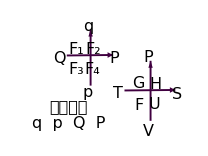
-Graphics-    其实，第几类是不重要的。
    ——   重要的是以什么量作为生成函数的自变量。
                                   以及怎么从生成函数得到正则变换
一个以  q, Q 为自变量的函数 U(q,Q)，
   满足“雅克比”非 0，必然对应于如下的正则变换：
                p_k=(∂U(q,Q))/(∂q_k),     P_k=-(∂U(q,Q))/(∂Q_k)
由第一式求得 Q(q,p)，再代入第二式求得 P(q,p)
或者由第二式求得  q(Q,P)，再代入第一式求得 p(Q,P)
  构成一个正则变换。
 思考：为何要加上“雅克比”非 0 这个条件？

生成函数：

ⅆ F_1=(∑_(k=1))^D p_k ⅆ q_k-(∑_(k=1))^D P_k ⅆ Q_k,        p_k=(∂F_1(q,Q))/(∂q_k),         P_k=-(∂F_1(q,Q))/(∂Q_k)

ⅆ F_2=(∑_(k=1))^D p_k ⅆ q_k+(∑_(k=1))^D Q_k ⅆ P_k,         p_k=(∂F_2(q,P))/(∂q_k),         Q_k=(∂F_2(q,P))/(∂P_k)

ⅆ F_3=-(∑_(k=1))^D q_k ⅆ p_k-(∑_(k=1))^D P_k ⅆ Q_k,     q_k=-(∂F_3(p,Q))/(∂p_k),    P_k=-(∂F_3(p,Q))/(∂Q_k)

ⅆ F_4=-(∑_(k=1))^D q_k ⅆ p_k+(∑_(k=1))^D Q_k ⅆ P_k,      q_k=-(∂F_4(p,P))/(∂p_k),    Q_k=(∂F_4(p,P))/(∂P_k)

热力学特性函数：(Good  Physicists  Have  Studied  Under  Very  Fine  Teacher)

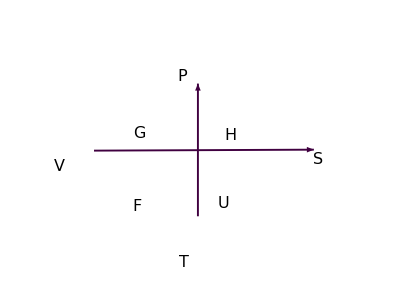
-Graphics-  ⅆG=V ⅆP-S ⅆT,              V=((∂G)/(∂P))_T,         S=-((∂G)/(∂T))_P ,          G(P,T)    特性函数
ⅆH=V ⅆP+T ⅆS,             V=((∂H)/(∂S))_P,         T=((∂H)/(∂P))_S,             H(P,S)    特性函数
ⅆU=-P ⅆV +T ⅆS,        P=-((∂U)/(∂V))_S,      T=((∂U)/(∂S))_V,            U(V,S)    特性函数 
ⅆF=-P ⅆV -S ⅆT,         P=-((∂F)/(∂V))_T,       S=-((∂F)/(∂T))_V,        F(V,T)    特性函数

## § 3.3 薛定谔方程 诶伦费斯特定理 位力定理

本节再通过一简单例子体验哈密顿力学形式的妙处。再次回答“既生瑜何生亮”问题。

### § 3.3.1 薛定谔方程

如何从哈密顿量“导出”（其实是“变出”，“萌出”）薛定谔方程。

以后还会用经典力学的其他形式，“弄出”薛定谔方程。

这一点在牛顿力学似乎是不可想象的，尽管本节的这些做法多少有点事后诸葛的味道。

—— 有理有据的做法将在第六章讨论。

假设单一个粒子在势场 U(x,y,z) 中运动。其拉格朗日量 (Lagrangian) 为

L=m/2((ẋ)^2+(ẏ)^2+(ż)^2)-U(x,y,z)

其哈密顿量为（以下是从拉格朗日量求哈密顿量的一般步骤）

p_k=(∂L)/(∂(ṡ)_k)=m (ṡ)_k          （先求广义动量，要通过此式反过来消去广义速度）

H=(∑_(k=1))^3(∂L)/(∂(ṡ)_k)(ṡ)_k-L        （为何要这样写而不是直接写出能量表达式 T+U？）

H=(p_x^2+p_y^2+p_z^2)/(2m)+U(x,y,z)

接着，是从经典到量子的方案：作以下代换

H ⟶ ⅈ ℏ ∂/(∂t),   p_x=-ⅈ ℏ ∂/(∂x),   p_y=-ⅈ ℏ ∂/(∂y),    p_z=-ⅈ ℏ ∂/(∂z)

其中 ℏ=h/(2π)，h 为 Plank 常数，其中 p_x, p_y, p_z 为正则动量（就是通过拉格朗日量求得的广义动量）。

再引入薛定谔波函数 ψ(x,y,z,t) ，让算符等式作用于波函数，从而

H=(p_x^2+p_y^2+p_z^2)/(2m)+U(x,y,z)

⇕

ⅈ ℏ ∂/(∂t)ψ={1/(2m)[(-ⅈ ℏ ∂/(∂x))(-ⅈ ℏ ∂/(∂x))+(-ⅈ ℏ ∂/(∂y))(-ⅈ ℏ ∂/(∂y))+(-ⅈ ℏ ∂/(∂z))(-ⅈ ℏ ∂/(∂z))]+ U} ψ

整理即得薛定谔方程

ⅈ ℏ ∂/(∂t)ψ=-ℏ^2/(2m)∇^2 ψ + U ψ                其中：∇^2 ψ=(∂^2 ψ)/(∂x^2)+(∂^2 ψ)/(∂y^2)+(∂^2 ψ)/(∂z^2)

当然，这里只是一点取巧，没有解释为何要作物理量到算符的替代（步子跨得有点大）。

更内在（密切）的关联还需要哈密顿-雅可比方程和正则变换（下半学期讨论，第六章）。

但至少，哈密顿力学展示了经典与量子力学的简单对应关系。

### § 3.3.2 诶伦费斯特定理

量子力学中，薛定谔波函数 ψ(x,y,z,t) 的模的平方被认为是几率密度。

例如，对一维问题， 𝒫(x,t)=ψ^*(x,t)ψ(x,t)， 量 𝒫(x,t)ⅆx 被认为是粒子出现在 x 到 x+ⅆx 的概率

因为是概率描述，故量子力学中通常不说物理量的值是多少，而是说它的期待值（也称平均值）是多少。

对任一个物理量，哈密顿力学认为总可以写成相空间坐标（正则坐标和正则动量）的函数。

因此，在量子力学中，求物理量的期待值就有了如下规范步骤

写出代表物理量的相空间变量的函数：f(x,y,z,p_x,p_y,p_z)

用算符替代相空间变量：x, y, z, p_(x,), p_y, p_z

如果波函数以位置坐标的函数形式出现（坐标表象），则对应于坐标 x, y,z 的“算符”就是坐标本身

而与其共轭的正则动量则以：p_x=-ⅈ ℏ ∂/(∂x),   p_y=-ⅈ ℏ ∂/(∂y),    p_z=-ⅈ ℏ ∂/(∂z) 替代

当然波函数也可以以正则动量的函数形式出现（动量表象），这时 p_(x,), p_y, p_z 的算符就是本身，坐标反而是以算符形式出现

物理量的期待值由下式计算（对于在坐标表象中的波函数，波函数表示为位置坐标的函数）

⟨f⟩=∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ψ^*f(x,y,z,-ⅈ ℏ ∂/(∂x),-ⅈ ℏ ∂/(∂y),-ⅈ ℏ ∂/(∂z))ψⅆxⅆyⅆz

其中已假设波函数是归一化的，即：∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ψ^*ψⅆxⅆyⅆz=1

例如，角动量的 z 分量在经典力学中为 L_z=(e⃗)_z·(r⃗×p⃗)=x p_y-y p_x，  (r⃗×p⃗)_k=ϵ_(k i j)r_i p_j,   ϵ_(k i j)为 Levi-Civita 三阶反对称张量

而量子力学中，角动量 z 分量的期待值为

⟨L_z⟩=-ⅈ ℏ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ψ^*[x ∂/(∂y)-y∂/(∂x)]ψⅆxⅆyⅆz     这里用的是坐标表象中的波函数，故：p_x=-ⅈ ℏ ∂/(∂x),   p_y=-ⅈ ℏ ∂/(∂y)

既然量子力学中求的是期待值，就可能会有偏差，均方根偏差定义为

Δ f=√(∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ (ψ^*[f(x,y,z,-ⅈ ℏ ∂/(∂x),-ⅈ ℏ ∂/(∂y),-ⅈ ℏ ∂/(∂z))-⟨f⟩])^2 ψⅆxⅆyⅆz)

现在，让我们来回顾总结一下这里的量子力学是怎么计算物理量的。

首先，写出哈密顿量 H，对它做一些替换（如正则动量 p 变成算符，哈密顿量 H 也变成算符），

得到量子力学（薛定谔）方程（波函数满足的微分方程）

接着，算出波函数 ψ，利用波函数的概率假设，

最后，遵循一些规范的计算步骤（见上面的 1, 2, 3），就能计算物理量的期待值。

——  忙个不亦乐乎。与经典力学的差别不是一般的大。

因而，就有了一个问题：这些计算，是否在某些极限下，能退化到与经典计算一致，

即，物理量的期待值  ⟨f⟩  退化为经典力学中相空间的函数值 f(q,p)，均方根偏差 Δ f→0。

（至于什么情况下这个期待值趋近于经典值，对不同体系可以不同。）

毕竟，“历史已经并将继续证明”，经典力学的结果在某些极限下是正确的。   咋整？咋证？

诶伦费斯特定理说：在某种极限下，经典力学的哈密顿方程在量子力学中也是成立的。

有点拗口，什么意思？——  也就是量子力学求出来的那些期待值，也满足哈密顿方程。

更明白一点，就是，量子力学和经典力学结果在某些极限下趋于一致。这就实现了“软着陆”或“平稳过渡”。

诶伦费斯特定理：

对哈密顿的一般形式：H=(p_x^2+p_y^2+p_z^2)/(2m)+U(x,y,z)   （一般形式指的是势场可以是任意的）

位置和动量的期待值服从以下类经典哈密顿方程：

(ⅆ⟨x_i⟩)/ⅆt=⟨(∂H(x,y,z,p_x,p_y,p_z))/(∂p_i)⟩,               (ⅆ⟨p_i⟩)/ⅆt=-⟨(∂H(x,y,z,p_x,p_y,p_z))/(∂x_i)⟩

其中 i=1,2,3, x_1=x, x_2=y, x_3=z, p_1=p_x 等等。

两个方程的等式右边是先对经典哈密顿求偏导，再对正则动量做以下替换（设波函数在坐标表象中）：

p_x=-ⅈ ℏ ∂/(∂x),   p_y=-ⅈ ℏ ∂/(∂y),    p_z=-ⅈ ℏ ∂/(∂z) ，   最后求期待值。

这个定理在量子力学中会给予证明。

在这里讨论这个定理，只是表明将经典力学写成哈密顿形式（相空间、哈密顿力学）

不仅方便“搞出”量子力学，而且还方便“弄出”经典和量子之间的联系 ——  经典是量子的某种极限

——  再次回答了 “既生瑜，何生亮？”

特别注意，类经典哈密顿方程等式右边的意义

⟨(∂H(x,y,z,p_x,p_y,p_z))/(∂x_i)⟩≠(∂H(⟨x⟩,⟨y⟩,⟨z⟩,⟨p_x⟩,⟨p_y⟩,⟨p_z⟩))/(∂⟨x_i⟩)

诶伦费斯特定理并不具体回答什么条件（如粒子质量、数密度、温度等）才能满足经典极限。

诶伦费斯特并没有证明

ⅆ/ⅆt⟨(∂L(x,y,z,v_x,v_y,v_z))/(∂v_i)⟩-⟨(∂L(x,y,z,v_x,v_y,v_z))/(∂x_i)⟩=0

### § 3.3.3 位力定理

位力定理表明：在一定条件下，动能的长时间平均值，与势能的长时间平均值之间有一定的关系。

统计力学将会讨论这个定理的一些应用（如位力定理加上能量均分定理，可以导出理想气体的状态方程）。

这里只是为学习哈密顿力学的应用。体会哈密顿力学的多一个优点。

简单起见，在 s-系中讨论问题。这时哈密顿可以写成：H=T+U，

其中 T 是广义动量 p 的齐次二次函数，U 仅依赖于坐标和时间（不依赖于动量）

定义相空间函数：χ=(∑_(k=1))^D q_k p_k，其时间导数为

ⅆχ/ⅆt=(∑_(k=1))^D(p_k(q̇)_k+q_k(ṗ)_k)=(∑_(k=1))^D(p_k(∂H)/(∂p_k)-q_k(∂H)/(∂q_k))=2T-(∑_(k=1))^D q_k(∂H)/(∂q_k)

这里利用了哈密顿方程式（紫色和绿色部分）、势能 U 与动量 p 无关，

而动能是 p 的齐次二次函数，故：(∑_(k=1))^D p_k(∂H)/(∂p_k)=(∑_(k=1))^D p_k(∂T)/(∂p_k)=2T

任何物理量 f(q,p) 的长时间平均值定义为（注意这里的 ⟨·⟩ 不是上一小节的期待值）

⟨f⟩=lim_(τ→∞) 1/τ∫_0^τ f[q(t),p(t)]ⅆt

现在，求 χ 的长时间平均值。

ⅆχ/ⅆt=2T-(∑_(k=1))^D q_k(∂H)/(∂q_k)      两边同时对 t 积分   ∫_0^τ  再除以 τ 最后求极限

左=lim_(τ→∞) 1/τ{(χ[q(τ),p(τ)]-χ[q(0),p(0)])_有限}=右=⟨2T⟩-⟨(∑_(k=1))^D q_k(∂H)/(∂q_k)⟩

因为在任何时刻，动量和坐标都是有限的（考虑束缚态），因此上式左边为 0， 从而

⟨2T⟩=⟨(∑_(k=1))^D q_k(∂H)/(∂q_k)⟩    (⟹_动能与位置坐标无关)^对一般体系    ⟨2T⟩=⟨(∑_(k=1))^D q_k(∂U)/(∂q_k)⟩=-⟨(∑_(k=1))^D s_k F_k⟩

其中利用了 动能与位置坐标无关：(∂H)/(∂q_k)=(∂(T+U))/(∂q_k)=(∂U)/(∂q_k)

并且利用保守力公式：F_k=-(∂U)/(∂q_k)， 即：F⃗=-∇U   （记得我们在 s-系中讨论）

写成矢量形式：  ⟨2T⟩=⟨(∑_(n=1))^N(r⃗)_n·(∇_n U)⟩ =-⟨(∑_(n=1))^N(r⃗)_n·(F⃗)_n⟩           N 为质点数

上式称为位力定理 (virial theorem)。上式右边称为 virial of Clausius.

有心力场中的质点

如果一个质点在中心力场中运动，如地球绕太阳转。

这时质点感受到的势能为 U=U(r)，其中 r  为质点到力中心的距离。

由位力定理

⟨2T⟩=⟨r⃗·(∇U)⟩=⟨r ⅆU/ⅆr⟩

若假设势能为：U(r)=A/r^n， 则  r ⅆU/ⅆr=-n U

⟨2T⟩=⟨-n U⟩   ⟹   ⟨T⟩=-n/2⟨U⟩

例如对引力势或静电势，

n=1，位力定理表明： 2⟨T⟩=-⟨U⟩

这里对束缚态而言，因为位力定理的证明用到了“任何时刻，动量和坐标都是有限”

机械能    E=⟨E⟩=⟨T⟩+⟨U⟩=(n-2)/n⟨T⟩

n=1 时，U=A/r，这时  E=-⟨T⟩，束缚态总能为负值

n=-α<0 时，U=A r^α，这时  E=(α+2)/α⟨T⟩>0，束缚态总能为正值

位力定理与理想状态气体方程

考虑体积为 V 的容器中，由大量无相互作用气体分子构成的理想气体

气体分子仅受容器器壁碰撞：ⅆ F⃗=-p n⃗ ⅆS    其中 p 是压强，n⃗ 是器壁外法向

哈密顿量：H=∑_i ((p⃗)_i^2)/(2m)+U(r⃗)

这里用 U(r⃗) 表示器壁碰撞力对应的势能， r⃗ 表示 (r⃗)_1, (r⃗)_2, , …,(r⃗)_n

思考：为什么要引进势能 U(r⃗)？碰撞力能引进势能吗？ 为了用位力定理，假设器壁对气体分子作用势模型

由位力定理：  ⟨2T⟩=-⟨(∑_(n=1))^N(r⃗)_n·(F⃗)_n⟩=-∮_S r⃗· ⅆ F⃗=-∮_S  r⃗·(-p n⃗ ⅆS)

⟹    2⟨T⟩=p∮_S  r⃗·n⃗ ⅆS=p∫_V ∇·r⃗ⅆV=3p V                             T 表示动能，绝对温度记为 Θ

而对单原子气体分子能量均分定理：⟨T⟩=N (3×1/2 k Θ )            其中 N 为气体分子数，Θ 为绝对温度

从而有理想气体状态方程： p V=N k Θ

### § 3.3.4 例题

例 3.3.01

一带电质点电磁场中运动，其拉格朗日量写成（§ 2.1.5   (1.8) 式）

L=1/2 m(v⃗)^2-q_e Φ(r⃗,t)+q_e v⃗·A⃗(r⃗,t),      q_e  为质点电荷

(a) 写出质点运动的广义能量函数和哈密顿量

(b) 试证其哈密顿方程可写成以下矢量形式

v⃗=(∂H)/(∂(p⃗)_c),       OverDot[(p⃗)_c]=(∂H)/(∂r⃗),  其中 (p⃗)_c 为正则动量， (p⃗)_c≠m v⃗

(c)  试证明第一个哈密顿方程建立了机械动量和正则动量之关系

(d)  试通过算符代换建立电磁场中运动的带电粒子的薛定谔方程

解：

(a)   拉格朗日量： L=1/2 m(v⃗)^2-q_e Φ(r⃗,t)+q_e  v⃗·A⃗(r⃗,t)

广义（正则）动量： (p⃗)_c=(∂L(r⃗,v⃗,t))/(∂ v⃗)            这里直接写成矢量形式
=m v⃗+q_e A⃗(r⃗,t)=(p⃗)_m+q_e A⃗(r⃗,t),               (p⃗)_m 为机械动量

广义能量函数：H=(∂L(r⃗,v⃗,t))/(∂ v⃗)·v⃗-L=(p⃗)_c·v⃗-L=1/2 m(v⃗)^2+q_e Φ(r⃗,t)

广义速度表示为广义动量（正则动量）：v⃗=((p⃗)_c-q_e A⃗(r⃗,t))/m

广义速度与正则动量并非仅差一个质量常数

代入广义能量函数即得

哈密顿量：H=1/(2m)[(p⃗)_c-q_e A⃗(r⃗,t)]·[(p⃗)_c-q_e A⃗(r⃗,t)]+q_e Φ(r⃗,t)

注意这时广义能量函数  H=1/2 m(v⃗)^2+q_e Φ(r⃗,t)  貌似是动能与势能之和

但哈密顿量并不等于   (p⃗)^2/(2m)+q_e Φ(r⃗,t)

哈密顿量是把广义能量函数写成 q,p,t 的函数，

其中 p 是广义动量，由 L 对 q̇ 的偏导数定义

(b) 第一组哈密顿方程

ẋ=(∂H)/(∂p_(c x)),  ẏ=(∂H)/(∂p_(c y)),   ż=(∂H)/(∂p_(c z)),  注意 是对广义动量（正则动量） (p⃗)_c 求偏导
不是对机械动量 p⃗ 求偏导

写成矢量形式：OverDot[r⃗]=(∂H)/(∂(p⃗)_c)   ⟹^(代入 H 的表达式)    v⃗=((p⃗)_c-q_e A⃗(r⃗,t))/m

类似地，第二组哈密顿方程可写成：      OverDot[p⃗]_c=-(∂H)/(∂r⃗)

(c)  上一小题结果表明第一组哈密顿方程其实就是：

v⃗=((p⃗)_c-q_e A⃗(r⃗,t))/m       表征广义速度与广义（正则）动量的关系

注意：  p⃗=m v⃗,    (p⃗)_c=m v⃗+q_e A⃗(r⃗,t)

拉格朗日力学中的一组定义  变成  哈密顿力学中的第一组哈密顿方程

(d)  对哈密顿量做替代：(p⃗)_c   ⟶  -ⅈ ℏ∇ 即得薛定谔方程

ⅈ ℏ(∂ψ)/(∂t)=1/(2m)[-ⅈℏ ∇-q_eA⃗(r⃗,t)]·[-ⅈℏ ∇-q_eA⃗(r⃗,t)]ψ+q_e Φ(r⃗,t)ψ

注意是将正则动量 (p⃗)_c 替代为算符，而非对机械动量 (p⃗)_m=m v⃗ 做替代。

注意绿色算符中的 -ⅈ ℏ ∇ 不但作用于波函数 ψ，

同时还作用于其右边中括号内的紫色 A⃗(r⃗,t)

即，φ⃗=[-ⅈℏ ∇-q_eA⃗(r⃗,t)]ψ,      [-ⅈℏ ∇-q_eA⃗(r⃗,t)]· φ⃗

例 3.3.02

已知哈密顿量 H(q,p,t) 并且哈密顿方程为

(q̇)_k=(∂H(q,p,t))/(∂p_k),  (ṗ)_k=-(∂H(q,p,t))/(∂q_k),  Ḣ=(∂H(q,p,t))/(∂t)

(a) 试写出拉格朗日量 L(q,p,t)

(b) 假设上述第一个方程可求得 p_k=p_k(q,q̇,t)，试求拉格朗日量 L(q,q̇,t)

(c)  通过全微分 ⅆL 反导出拉格朗日方程

p_k=(∂L(q,q̇,t))/(∂(q̇)_k),  (ṗ)_k=(∂L(q,q̇,t))/(∂q_k),  Ḣ=-(∂L(q,q̇,t))/(∂t)

解：

(a)   哈密顿量其实就是广义能量函数，与拉格朗日量之间差一个勒让德变换，因此

H=(∑_(k=1))^D (∂L)/(∂(q̇)_k)(q̇)_k-L       ⟹     L=(∑_(k=1))^D p_k(q̇)_k-H

从而：L(q,p,t)=(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)

L(q,p,t)=(∑_(k=1))^D p_k(∂H(q,p,t))/(∂p_k)-H(q,p,t)     写成  q,p,t 的函数

▲    写 H=(∑_(k=1))^D p_k(q̇)_k-L          ?? p_k(ṗ)_k, ?? q_k(q̇)_k, ?? q_k(ṗ)_k

求和式是能量量纲，必然一个 p 和 一个 q，其中有一个对时间求导

另一方面：哈密顿量是广义能量函数中以 p_k 替代 (q̇)_k，所以求和式是 p_k (q̇)_k

(b)    哈密顿方程   (q̇)_k=(∂H(q,p,t))/(∂p_k)=  (q̇)_k(q,p,t)          ⟹^题设可逆   p_k=p_k(q,q̇,t)

拉格朗日量（应该是  q,q̇,t  的函数）

L(q,q̇,t)=(∑_(k=1))^D p_k(q,q̇,t)(q̇)_k-H(q,p(q,q̇,t),t)

Quiz：  (q̇)_k=(q̇)_k(q,p,t)  可以求得反函数 p_k=p_k(q,q̇,t) 的充要条件？雅克比

(c)  这里 L 有两种形式：

(1)        L(q,p,t)=(∑_(k=1))^D p_k(q̇)_k-H(q,p,t)；      (2)          L=L(q,q̇,t)

现通过这两式求全微分来推导拉格朗日 方程（模仿哈密顿方程的导出方法）

第(1)式：ⅆL=(∑_(k=1))^D (p_k ⅆ(q̇)_k+(q̇)_k ⅆ p_k)-ⅆH(q,p,t) 
=(∑_(k=1))^D (p_k ⅆ(q̇)_k+(q̇)_k ⅆ p_k-(∂H)/(∂q_k)ⅆ q_k-(∂H)/(∂p_k)ⅆ p_k)-(∂H(q,p,t))/(∂t)ⅆt 
=(∑_(k=1))^D (p_k ⅆ(q̇)_k+(q̇)_k ⅆ p_k+(ṗ)_k ⅆ q_k-(q̇)_k ⅆ p_k)-(∂H(q,p,t))/(∂t)ⅆt
=(∑_(k=1))^D (p_k ⅆ(q̇)_k+(ṗ)_k ⅆ q_k)-Ḣ ⅆt      H 写成 q,p,t 的函数时，(∂H(q,p,t))/(∂t)=Ḣ

第(2)式：ⅆL(q,q̇,t)=(∑_(k=1))^D ((∂L(q,q̇,t))/(∂(q̇)_k)ⅆ(q̇)_k+(∂L(q,q̇,t))/(∂q_k)ⅆ q_k)+(∂L(q,q̇,t))/(∂t)ⅆt

比较紫、蓝两式：p_k=(∂L(q,q̇,t))/(∂(q̇)_k)， (ṗ)_k=(∂L(q,q̇,t))/(∂q_k)， Ḣ=-(∂L(q,q̇,t))/(∂t)

上三式即为拉格朗日方程，前两式可归并为：ⅆ/ⅆt(∂L(q,q̇,t))/(∂(q̇)_k)-(∂L(q,q̇,t))/(∂q_k)=0

这个问题表明：

拉格朗日方程也可以像哈密顿方程那样，写成两组方程，但对称性晦涩

p_k=(∂L(q,q̇,t))/(∂(q̇)_k)，    (ṗ)_k=(∂L(q,q̇,t))/(∂q_k)            （第一组一般当成广义动量的定义了）

而哈密顿方程的对称性明显（除了一个负号，这个负号在泊松括号形式中自然隐身了）：

(q̇)_k=(∂H(q,p,t))/(∂p_k),    (ṗ)_k=-(∂H(q,p,t))/(∂q_k)

等价的理论并不一定同样好，哈密顿形式似乎更能体现对称之美（核心价值观之美）。

例 3.3.03

已知如下两个拉格朗日量 L(q,q̇,t)和  L'(q,q̇,t)给出相同的拉格朗日方程

L'(q,q̇,t)= L(q,q̇,t)+(ⅆf(q,t))/ⅆt

(a) 两个拉格朗日量对应的广义动量分别为

p_k=(∂L(q,q̇,t))/(∂(q̇)_k),     p'_k=(∂L'(q,q̇,t))/(∂(q̇)_k)

试求 p'_k, p_k 和 f(q,t) 之间的关系

(b) 试求对应于L'(q,q̇,t)的广义能量函数 H'(q,q̇,t) 、对应于 L(q,q̇,t)的

广义能量函数 H(q,q̇,t) 和 f(q,t)三者 之间的关系

(c)  假设 H(q,q̇,t) 可化为哈密顿量 H(q,p,t) ，试将 H'(q,q̇,t) 写成“哈密顿量” H'(q,p,t)

(d)  利用 p 和 p' 的关系将“哈密顿量” H'(q,p,t)改写为哈密顿量 H'(q,p',t)

(e)  设原哈密顿量的哈密顿方程为

(q̇)_k=(∂H(q,p,t))/(∂p_k),  (ṗ)_k=-(∂H(q,p,t))/(∂q_k)

试证新哈密顿量服从相同形式的方程

(q̇)_k=(∂H'(q,p',t))/(∂p_k),  (ṗ')_k=-(∂H'(q,p',t))/(∂q_k)

解：

依题意： L'(q,q̇,t)= L(q,q̇,t)+(ⅆf(q,t))/ⅆt

即：    L'(q,q̇,t)= L(q,q̇,t)+∑_k (∂f(q,t))/(∂q_k)(q̇)_k+(∂f(q,t))/(∂t)

(a)   p'_k=(∂L'(q,q̇,t))/(∂(q̇)_k)=(∂L(q,q̇,t))/(∂(q̇)_k)+(∂f(q,t))/(∂q_k)

p'_k=p_k+ (∂f(q,t))/(∂q_k)    两个广义动量之间的关系

(b)    H'(q,q̇,t) =∑_k p'_k(q̇)_k-L'(q,q̇,t)
=∑_k [p_k+ (∂f(q,t))/(∂q_k)](q̇)_k-[L(q,q̇,t)+∑_k (∂f(q,t))/(∂q_k)(q̇)_k+(∂f(q,t))/(∂t)]
=∑_k p_k(q̇)_k-L(q,q̇,t)-(∂f(q,t))/(∂t)=H(q,q̇,t)-(∂f(q,t))/(∂t)

H'(q,q̇,t) =H(q,q̇,t)-(∂f(q,t))/(∂t)      两个广义能量函数之间的关系

(c)     利用   (q̇)_k=(q̇)_k(q,p,t)   可得：

H'(q,p,t) =H(q,p,t) -(∂f(q,t))/(∂t)

(d)    利用 p'_k=p_k+ (∂f(q,t))/(∂q_k) 消去 p_k，上式可化为

H'(q,p',t) =H(q,(p'-(∂f(q,t))/(∂q))_p,t) -(∂f(q,t))/(∂t)       两个哈密顿量函数之间的关系

(e)  最后，来看新哈密顿量对应的哈密顿方程是否与原来等价

(q̇)_k=^(？？)(∂H'(q,p',t))/(∂p'_k)，       (ṗ')_k=^(？？)-(∂H'(q,p',t))/(∂q_k)

利用(d) 得到的两个哈密顿量函数之间的关系

H'(q,p',t) =H(q,(p'-(∂f(q,t))/(∂q))_p,t) -(∂f(q,t))/(∂t)

((∂H'(q,p',t))/(∂p'_k)|)_(q, t)=(∂H(q,(p'-∂f/∂q)^p,t))/(∂p'_k)-(∂^2 f(q,t))/(∂p'_k∂t)       绿色项为 0，因为带撇系中 p ' 与 q 是独立的
=∑_j (∂H(q,p,t))/(∂p_j)(∂p_j(q,p',t))/(∂p'_k)       是在 q, t 不变下求的导数
=∑_j (∂H(q,p,t))/(∂p_j)δ_(j,k)      利用了：p_j=p'_j- (∂f(q,t))/(∂q_k)，注意p ' 与 q 是独立的
=(∂H(q,p,t))/(∂p_k)
=(q̇)_k                       大功告成之一：   (q̇)_k=(∂H'(q,p',t))/(∂p_k)  与  (q̇)_k=(∂H(q,p,t))/(∂p_k)  等价

((∂H'(q,p',t))/(∂q_k)|)_(p', t)=(∂H(q,(p'-∂f/∂q)^p,t))/(∂q_k)-(∂f(q,t))/(∂q_k∂t)     是在 p', t 不变下求的导数
=(∂H)/(∂q_k)+∑_j (∂H(q,p,t))/(∂p_j)(∂p_j(q,p',t))/(∂q_k)-(∂^2 f(q,t))/(∂q_k∂t)       利用：p_j=p'_j- (∂f(q,t))/(∂q_j)
=-(ṗ)_k+∑_j (q̇)_j(-(∂^2 f(q,t))/(∂q_k∂q_j))-(∂^2 f(q,t))/(∂q_k∂t)         利用：∑_j (q̇)_j∂/(∂q_j)[(∂f(q,t))/(∂q_k)]+∂/(∂t)[(∂f(q,t))/(∂q_k)]=ⅆ/ⅆt[(∂f(q,t))/(∂q_k)]
=-(ṗ)_k-ⅆ/ⅆt[(∂f(q,t))/(∂q_k)]
=-ⅆ/ⅆt[p_k+(∂f(q,t))/(∂q_k)]=(ṗ')_k       大功告成之二： (ṗ')_k=-(∂H'(q,p',t))/(∂q_k)  与  (ṗ)_k=-(∂H(q,p,t))/(∂q_k)  等价

这表明，等价的拉格朗日量得到相同的拉格朗日方程，

由等价的拉格朗日量导出的哈密顿量也等价（哈密顿方程相同）

## The end

G_Q_k^(2)(q,P)